```mathematica
pp[n_,z_]:=Product[ z/a!,{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
p2[n_,k_]:=Sum[(-1)^(k-j) Binomial[k,j] pp[n,j],{j,0,k}]
lLinnik[n_]:=Sum[(-1)^(k+1)/k p2[n,k],{k,1,Log[2,n]}]
Table[{n,ll[n,1],ll[n,2],l2[n,1],l2[n,2],lLinnik[n]},{n,2,100}]//TableForm
```

2 | 1/2 | 1 | 1/2 | 0 | 1/2
3 | 1/2 | 1 | 1/2 | 0 | 1/2
4 | 1/2 | 1 | 1/2 | 0 | 1/2
5 | 1/2 | 1 | 1/2 | 0 | 1/2
6 | 1/4 | 1 | 1/4 | 1/2 | 0
7 | 1/2 | 1 | 1/2 | 0 | 1/2
8 | 1/2 | 1 | 1/2 | 0 | 1/2
9 | 1/2 | 1 | 1/2 | 0 | 1/2
10 | 1/4 | 1 | 1/4 | 1/2 | 0
11 | 1/2 | 1 | 1/2 | 0 | 1/2
12 | 1/4 | 1 | 1/4 | 1/2 | 0
13 | 1/2 | 1 | 1/2 | 0 | 1/2
14 | 1/4 | 1 | 1/4 | 1/2 | 0
15 | 1/4 | 1 | 1/4 | 1/2 | 0
16 | 1/2 | 1 | 1/2 | 0 | 1/2
17 | 1/2 | 1 | 1/2 | 0 | 1/2
18 | 1/4 | 1 | 1/4 | 1/2 | 0
19 | 1/2 | 1 | 1/2 | 0 | 1/2
20 | 1/4 | 1 | 1/4 | 1/2 | 0
21 | 1/4 | 1 | 1/4 | 1/2 | 0
22 | 1/4 | 1 | 1/4 | 1/2 | 0
23 | 1/2 | 1 | 1/2 | 0 | 1/2
24 | 1/4 | 1 | 1/4 | 1/2 | 0
25 | 1/2 | 1 | 1/2 | 0 | 1/2
26 | 1/4 | 1 | 1/4 | 1/2 | 0
27 | 1/2 | 1 | 1/2 | 0 | 1/2
28 | 1/4 | 1 | 1/4 | 1/2 | 0
29 | 1/2 | 1 | 1/2 | 0 | 1/2
30 | 1/8 | 1 | 1/8 | 3/4 | 0
31 | 1/2 | 1 | 1/2 | 0 | 1/2
32 | 1/2 | 1 | 1/2 | 0 | 1/2
33 | 1/4 | 1 | 1/4 | 1/2 | 0
34 | 1/4 | 1 | 1/4 | 1/2 | 0
35 | 1/4 | 1 | 1/4 | 1/2 | 0
36 | 1/4 | 1 | 1/4 | 1/2 | 0
37 | 1/2 | 1 | 1/2 | 0 | 1/2
38 | 1/4 | 1 | 1/4 | 1/2 | 0
39 | 1/4 | 1 | 1/4 | 1/2 | 0
40 | 1/4 | 1 | 1/4 | 1/2 | 0
41 | 1/2 | 1 | 1/2 | 0 | 1/2
42 | 1/8 | 1 | 1/8 | 3/4 | 0
43 | 1/2 | 1 | 1/2 | 0 | 1/2
44 | 1/4 | 1 | 1/4 | 1/2 | 0
45 | 1/4 | 1 | 1/4 | 1/2 | 0
46 | 1/4 | 1 | 1/4 | 1/2 | 0
47 | 1/2 | 1 | 1/2 | 0 | 1/2
48 | 1/4 | 1 | 1/4 | 1/2 | 0
49 | 1/2 | 1 | 1/2 | 0 | 1/2
50 | 1/4 | 1 | 1/4 | 1/2 | 0
51 | 1/4 | 1 | 1/4 | 1/2 | 0
52 | 1/4 | 1 | 1/4 | 1/2 | 0
53 | 1/2 | 1 | 1/2 | 0 | 1/2
54 | 1/4 | 1 | 1/4 | 1/2 | 0
55 | 1/4 | 1 | 1/4 | 1/2 | 0
56 | 1/4 | 1 | 1/4 | 1/2 | 0
57 | 1/4 | 1 | 1/4 | 1/2 | 0
58 | 1/4 | 1 | 1/4 | 1/2 | 0
59 | 1/2 | 1 | 1/2 | 0 | 1/2
60 | 1/8 | 1 | 1/8 | 3/4 | 0
61 | 1/2 | 1 | 1/2 | 0 | 1/2
62 | 1/4 | 1 | 1/4 | 1/2 | 0
63 | 1/4 | 1 | 1/4 | 1/2 | 0
64 | 1/2 | 1 | 1/2 | 0 | 1/2
65 | 1/4 | 1 | 1/4 | 1/2 | 0
66 | 1/8 | 1 | 1/8 | 3/4 | 0
67 | 1/2 | 1 | 1/2 | 0 | 1/2
68 | 1/4 | 1 | 1/4 | 1/2 | 0
69 | 1/4 | 1 | 1/4 | 1/2 | 0
70 | 1/8 | 1 | 1/8 | 3/4 | 0
71 | 1/2 | 1 | 1/2 | 0 | 1/2
72 | 1/4 | 1 | 1/4 | 1/2 | 0
73 | 1/2 | 1 | 1/2 | 0 | 1/2
74 | 1/4 | 1 | 1/4 | 1/2 | 0
75 | 1/4 | 1 | 1/4 | 1/2 | 0
76 | 1/4 | 1 | 1/4 | 1/2 | 0
77 | 1/4 | 1 | 1/4 | 1/2 | 0
78 | 1/8 | 1 | 1/8 | 3/4 | 0
79 | 1/2 | 1 | 1/2 | 0 | 1/2
80 | 1/4 | 1 | 1/4 | 1/2 | 0
81 | 1/2 | 1 | 1/2 | 0 | 1/2
82 | 1/4 | 1 | 1/4 | 1/2 | 0
83 | 1/2 | 1 | 1/2 | 0 | 1/2
84 | 1/8 | 1 | 1/8 | 3/4 | 0
85 | 1/4 | 1 | 1/4 | 1/2 | 0
86 | 1/4 | 1 | 1/4 | 1/2 | 0
87 | 1/4 | 1 | 1/4 | 1/2 | 0
88 | 1/4 | 1 | 1/4 | 1/2 | 0
89 | 1/2 | 1 | 1/2 | 0 | 1/2
90 | 1/8 | 1 | 1/8 | 3/4 | 0
91 | 1/4 | 1 | 1/4 | 1/2 | 0
92 | 1/4 | 1 | 1/4 | 1/2 | 0
93 | 1/4 | 1 | 1/4 | 1/2 | 0
94 | 1/4 | 1 | 1/4 | 1/2 | 0
95 | 1/4 | 1 | 1/4 | 1/2 | 0
96 | 1/4 | 1 | 1/4 | 1/2 | 0
97 | 1/2 | 1 | 1/2 | 0 | 1/2
98 | 1/4 | 1 | 1/4 | 1/2 | 0
99 | 1/4 | 1 | 1/4 | 1/2 | 0
100 | 1/4 | 1 | 1/4 | 1/2 | 0

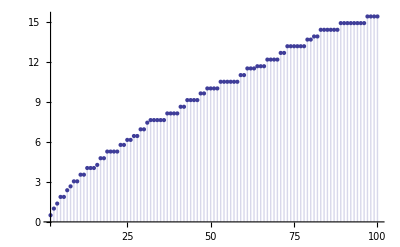

```mathematica
PI[n_, k_] := Sum[ll[j,1]( 1/k-PI[Floor[n/j],k+1]),{j,2,n}]
DiscretePlot[ PI[n,1],{n,2,100}]
```